```mathematica
Quit[]
```

```mathematica
<<init`
```

```mathematica
$UserBaseDirectory
```

/Users/yuichiro/Library/Mathematica

```mathematica
PhaseV[x_,p_]={-p,3p-β(β+3)x};
```

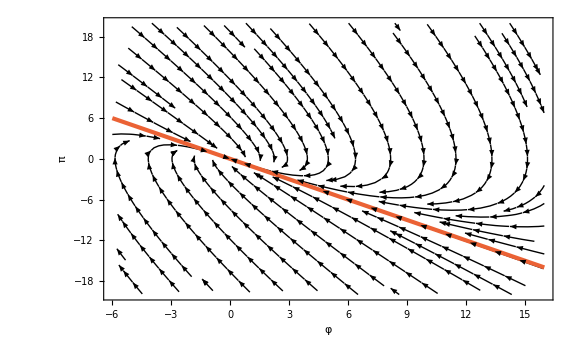

```mathematica
Show[StreamPlot[-PhaseV[x,p]/.{β->-1},{x,-6,16},{p,-20,20},AxesOrigin->{0,0},Axes->True,FrameLabel->{{π,None},{φ,β==-1}},PlotRange->{{-6,16},{-20,20}},StreamStyle->Black,StreamColorFunction->None],
Plot[β x/.{β->-1},{x,-6,16},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

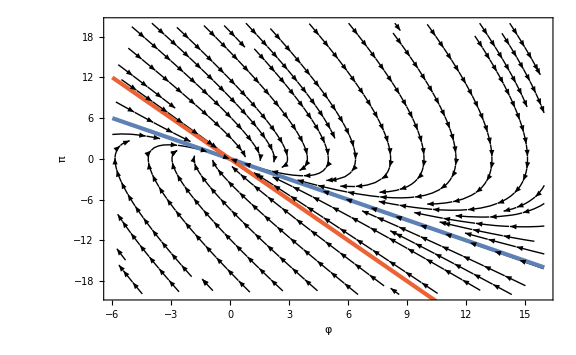

```mathematica
Show[StreamPlot[-PhaseV[x,p]/.{β->-2},{x,-6,16},{p,-20,20},AxesOrigin->{0,0},Axes->True,FrameLabel->{{π,None},{φ,β==-2}},PlotRange->{{-6,16},{-20,20}},StreamStyle->Black,StreamColorFunction->None],
Plot[{-(3+β)x/.{β->-2},β x/.{β->-2}},{x,-6,16},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[3],Color[4]}}]]
```

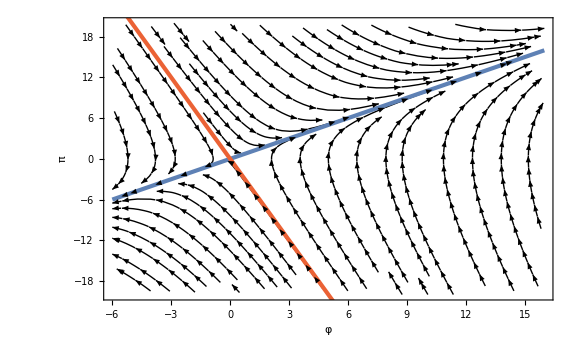

```mathematica
Show[StreamPlot[-PhaseV[x,p]/.{β->-4},{x,-6,16},{p,-20,20},AxesOrigin->{0,0},Axes->True,FrameLabel->{{π,None},{φ,β==-4}},PlotRange->{{-6,16},{-20,20}},StreamStyle->Black,StreamColorFunction->None],
Plot[{-(3+β)x/.{β->-4},β x/.{β->-4}},{x,-6,16},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[3],Color[4]}}]]
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

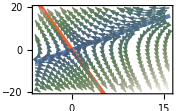
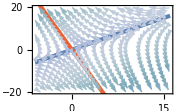
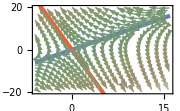
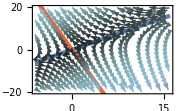
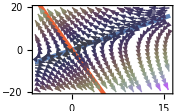
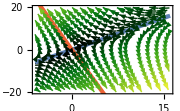
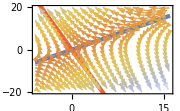
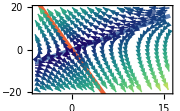

```mathematica
Table[Show[StreamPlot[PhaseV[x,p]/.{β->-4},{x,-6,16},{p,-20,20},AxesOrigin->{0,0},Axes->True,FrameLabel->{φ,π},PlotRange->{{-6,16},{-20,20}},StreamColorFunction->ColorData["Gradients"][[i]],ImageSize->Small],
Plot[{-(3+β)x/.{β->-4},β x/.{β->-4}},{x,-6,16},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[3],Color[4]}}]],{i,Length[ColorData["Gradients"]]}]
```